# Figure S3

### Standing variation experiment A small fraction of resistant strain (turbidostat - evolved), approx 1 : 1000 added to check the model without mutations

```mathematica
SetDirectory[NotebookDirectory[]]

SE[x_]:=If[Length[x]>1,Sqrt[Variance[x]/Length[x]],0]

SetOptions[{ListPlot,ListLogPlot,ListLinePlot,Histogram,ListDensityPlot},BaseStyle->FontSize->24,Frame->True,FrameStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}},AxesStyle->{{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}},{{Black,AbsoluteThickness[2]},{Black,AbsoluteThickness[2]}}}];
Clear[RemoveSpikes]
RemoveSpikes[d_]:=Module[{diff=Abs[Differences[d[[All,2]]]],eps=0.005},Select[Table[{d[[i]],If[i<Length[d]-1,If[diff[[i+1]]<eps && diff[[i]]<eps,True,False],If[diff[[i-1]]<eps,True,False]]},{i,Length[d]}],(#[[2]])&][[All,1]]]

Clear[DispPval]
DispPval[p_]:=Which[p<0.001,"<0.001",p<0.01,ToString[NumberForm[p,{2,4}]],p<0.1,ToString[NumberForm[p,{2,3}]],p<1,ToString[NumberForm[p,{2,2}]]]
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor

### import OD data and growth rates etc .

```mathematica
<<"mix_sensitive_and_RIF_resistant_newMUT_rep1-2_1_to_1000_ODvsTIME.mx";
dataRIFnewMUT12=dataprev;  (* use here RIF-uncorrected data because this is what the simulation tries to reproduce *)
<<"mix_sensitive_and_RIF_resistant_newMUT_rep1-2_1_to_1000.mx";
paramsRIFnewMUT12=alldata;

<<"mix_sensitive_and_CIP_resistant_1_to_1000_ODvsTIME_bkg_corrected.mx";
dataCIP=data;
<<"mix_sensitive_and_CIP_resistant_1_to_1000.mx";
paramsCIP=alldata;

<<"mix_sensitive_and_STR_resistant_new_new_1_to_1000_ODvsTIME.mx";
dataSTR3=data;
<<"mix_sensitive_and_STR_resistant_new_new_1_to_1000.mx";
paramsSTR3=alldata;

(* model parameters *)
odcrit=0.1;dilf=0.75;
noreps="1000"; (* number of replicate simulation *)
```

## RIF

### rpoB mutant D516Y, actual ratio WT: mutant 1000:1

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsRIFnewMUT12;
Length[vols]
tregrowths

RIFlambda="0.16";RIF0="0.023"; (* values should be the same as in "process_OD..." notebook *)
```

5

{8.77478,8.76897,8.58611,8.49839,9.37581}

### This runs the simulation. The mode adds RIF contribution to the OD, so this needs to be compared with uncorrected data (in the above, “dataRIFnewMUT12=dataprev” ensures this is the case)

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\RIF_standvar"]
Do[
name="START \" \"  \""<>NotebookDirectory[]<>"models\\turbidostat_standing_variation_for_Bayesian_RIF.exe\" standing_var_five"<>ToString[nn]<>" "<>ToString[vols[[nn]]]<>" "<>ToString[odinis[[nn]]]<>" "<>ToString[births[[nn,1]]]<>" "<>ToString[birthsres[[nn,1]]]<>" "<>ToString[birthsres[[nn,1]]]<>" "<>ToString[ainjs[[nn]]]<>" "<>ToString[tends[[nn]]]<>" "<>(*ToString[tregrowths[[nn]]]*)"100"<>" "<>ToString[odcrit dilf]<>" "<>noreps<>" 0.001  0.1  0.1 "<>RIF0<>" "<>RIFlambda<> " 0.75";
Print[name];
Run[name]
,{nn,Length[vols]}]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\RIF_standvar

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_RIF.exe" standing_var_five1 25.74 0.0021788 1.98877 2.02865 2.02865 4.82853 19.9965 100 0.075 1000 0.001  0.1  0.1 0.023 0.16 0.75

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_RIF.exe" standing_var_five2 25.55 0.00229147 2.00071 2.05385 2.05385 4.77881 19.9966 100 0.075 1000 0.001  0.1  0.1 0.023 0.16 0.75

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_RIF.exe" standing_var_five3 25.08 0.00267892 2.05494 1.98823 1.98823 4.57775 18.4878 100 0.075 1000 0.001  0.1  0.1 0.023 0.16 0.75

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_RIF.exe" standing_var_five4 25.58 0.00291549 2.02345 2.06909 2.06909 4.47614 18.4879 100 0.075 1000 0.001  0.1  0.1 0.023 0.16 0.75

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_RIF.exe" standing_var_five5 24.89 0.00277997 1.86728 1.91284 1.91284 5.01042 18.4879 100 0.075 1000 0.001  0.1  0.1 0.023 0.16 0.75

### Import the simulated OD vs time curves:

{1000,1000,1000,1000,1000}

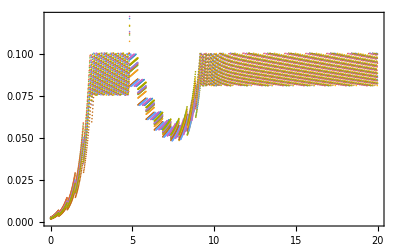

{{6,12,18,24,53,59,69,83,84,100,126,138,141,150,163,180,188,212,222,223,226,236,259,264,309,347,363,364,366,369,392,396,409,428,450,457,474,493,514,524,526,531,547,556,571,608,621,639,647,672,676,690,722,724,728,738,748,757,763,767,782,794,796,805,806,810,826,827,877,886,908,919,941,943,946,962,986},{32,64,116,130,150,169,261,282,390,404,415,433,481,484,485,499,553,560,640,726,739,810,842,856,875,935,943},{137,164,207,211,278,389,408,410,479,585,639,640,733,749,839,868,944},{28,56,76,92,102,110,121,136,144,155,204,215,217,247,283,286,291,316,359,361,373,377,378,384,386,396,424,437,440,444,446,467,515,552,603,620,622,625,711,755,760,765,882,946,947},{27,29,69,126,137,143,154,156,168,198,234,326,334,349,372,375,381,407,422,434,440,447,461,468,488,489,502,522,533,625,668,705,710,711,712,728,736,755,766,777,786,808,822,831,858,870,877,879,952,954,964}}

```mathematica
nns=Table[ReadList["models\\RIF_standvar\\std_var_n_standing_var_five"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[vols]}];
th=Table[Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[n,i]]];If[i==Length[nns[[n]]] || nns[[n,i+1,1]]<nns[[n,i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns[[n]]]}];th],{n,Length[nns]}];
Length[#]&/@th
ListPlot[th[[1,1;;10,All,{1,4}]]]

(* get indices of runs which agree within a given tolerance with the time to first OD=0.1 *)
simdist=Table[ReadList["models\\RIF_standvar\\std_var_distribution_standing_var_five"<>ToString[n]<>".dat",{Number,Number,Number,Number,Number}],{n,Length[vols]}];
bestthr=Table[Select[Table[{i,simdist[[k,i,2]]},{i,Length[simdist[[k]]]}],(Abs[#[[2]]-tfirstthr[[k]]]<0.05)&][[All,1]],{k,Length[vols]}]
```

#### Distribution of regrowth times (RIF):

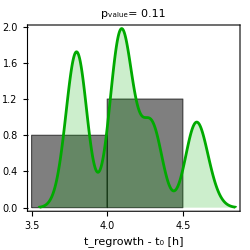

KS-test p-value: 0.113012

```mathematica
RegrowtTimeDistribution[name_]:=Module[{gr,pval,tmp,grth,grexp},
tmp=Flatten[Table[If[NumberQ[#[[1]]],#[[1]]-ainjs[[i]],#]&/@Select[simdist[[i]],(Abs[#[[2]]-tfirstthr[[i]]]<0.1)&],{i,Length[simdist]}]];
grth=SmoothHistogram[Select[tmp,((NumberQ[#])&)][[All]],Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom];
grexp=Histogram[Select[tregrowths-ainjs,(#≠∞)&],{3,6,1/2},"PDF",ChartStyle->Opacity[0.5,Black]];
gr=Show[{grexp,grth}(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->250(*,ChartLegends->{"sim","exp"}*),PlotRange->{{3,7},{0,All}},PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Select[tmp[[All]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
pval=KolmogorovSmirnovTest[Select[tmp[[All]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]];
Print["KS-test p-value: ",pval]];

RegrowtTimeDistribution["RIF_spike_in_Pregrowth.png"]
```

### OD vs time curves - experiment and modelling:

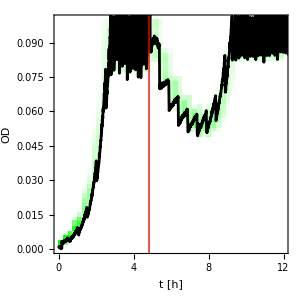

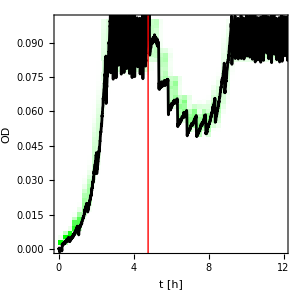

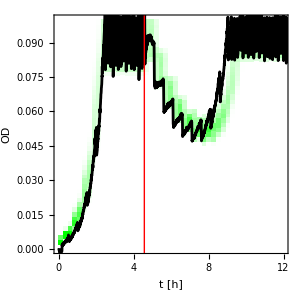

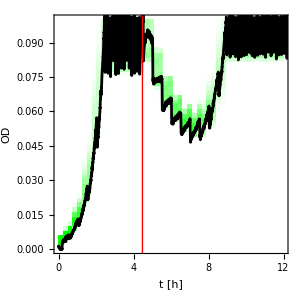

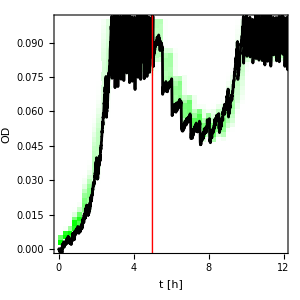

```mathematica
Do[pl=Show[ListDensityPlot[Transpose[BinCounts[Flatten[th[[k,All,All,{1,4}]],1],{0,12,0.25},{0,0.1,0.002}]],ColorFunction->(RGBColor[Max[0,1-2#],1,Max[0,1-2#]]&),PlotRange->All,InterpolationOrder->0,DataRange->{{0,12},{0,0.1}}],ListPlot[dataRIFnewMUT12[[k,"ods"]],Joined->True,PlotStyle->Black],ImageSize->300,BaseStyle->FontSize->24,FrameLabel->{"t [h]","OD"},Epilog->{Red,Line[{{ainjs[[k]],-0.1},{ainjs[[k]],1}}]}];Export[NotebookDirectory[]<>"\\figures\\RIF_spikein_model_and_exp"<>ToString[k]<>".png",pl,"PNG"];Print[pl],{k,1,Length[vols]}]
```

## CIP

### gyrA mutant S83L, WT:mutant ratio 1000:1

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsCIP;
Length[vols]
tregrowths
```

4

{14.9979,14.5129,13.8549,13.7344}

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\CIP_standvar"]
Do[
name="START \" \" "<>cmdpars<>" \""<>NotebookDirectory[]<>"models\\turbidostat_standing_variation_for_Bayesian_CIP.exe\" standing_var"<>ToString[nn]<>" "<>ToString[vols[[nn]]]<>" "<>ToString[odinis[[nn]]]<>" "<>ToString[births[[nn,1]]]<>" "<>ToString[births[[nn,1]]]<>" "<>ToString[birthsres[[nn,1]]]<>" "<>ToString[ainjs[[nn]]]<>" "<>ToString[tends[[nn]]]<>" "<>(*ToString[tregrowths[[nn]]]*)"100"<>" "<>ToString[odcrit dilf]<>" "<>noreps<>" 0.001  0.1  0.1   2.0";
Print[name];
Run[name]
,{nn,4}]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\CIP_standvar

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_CIP.exe" standing_var1 26.55 0.0104424 1.74555 1.74555 1.27613 3.98967 22.9088 100 0.075 1000 0.001  0.1  0.1   2.0

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_CIP.exe" standing_var2 25.54 0.0113475 1.80872 1.80872 1.36 3.99892 22.9088 100 0.075 1000 0.001  0.1  0.1   2.0

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_CIP.exe" standing_var3 26.29 0.0093451 1.90092 1.90092 1.46382 4.02886 22.9088 100 0.075 1000 0.001  0.1  0.1   2.0

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_CIP.exe" standing_var4 28. 0.00946619 1.78896 1.78896 1.39126 4.0825 22.9088 100 0.075 1000 0.001  0.1  0.1   2.0

{1000,1000,1000,1000}

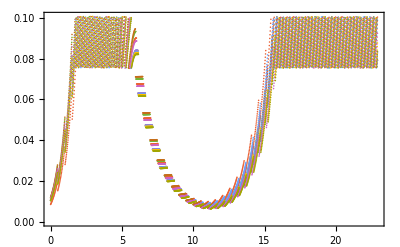

```mathematica
nns=Table[ReadList["models\\CIP_standvar\\std_var_n_standing_var"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,4}];
th=Table[Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[n,i]]];If[i==Length[nns[[n]]] || nns[[n,i+1,1]]<nns[[n,i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns[[n]]]}];th],{n,Length[nns]}];
Length[#]&/@th
ListPlot[th[[1,1;;10,All,{1,4}]]]

(* get indices of runs which agree within a given tolerance with the time to first OD=0.1 *)
simdist=Table[ReadList["models\\CIP_standvar\\std_var_distribution_standing_var"<>ToString[n]<>".dat",{Number,Number,Number,Number,Number}],{n,Length[vols]}];
bestthr=Table[Select[Table[{i,simdist[[k,i,2]]},{i,Length[simdist[[k]]]}],(Abs[#[[2]]-tfirstthr[[k]]]<0.05)&][[All,1]],{k,Length[vols]}]
```

#### Distribution of regrowth times (CIP)

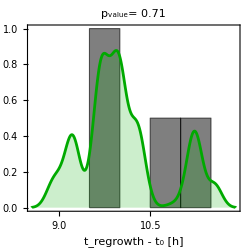

KS-test p-value: 0.706958

```mathematica
Clear[RegrowtTimeDistribution]
RegrowtTimeDistribution[name_]:=Module[{gr,pval,tmp,grth,grexp},
tmp=Flatten[Table[If[NumberQ[#[[1]]],#[[1]]-ainjs[[i]],#]&/@Select[simdist[[i]],(Abs[#[[2]]-tfirstthr[[i]]]<0.1)&],{i,Length[simdist]}]];
grth=SmoothHistogram[Select[tmp,((NumberQ[#])&)][[All]],Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom];
grexp=Histogram[Select[tregrowths-ainjs,(#≠∞)&],{8,14,1/2},"PDF",ChartStyle->Opacity[0.5,Black]];
gr=Show[{grexp,grth}(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->250(*,ChartLegends->{"sim","exp"}*),PlotRange->{{8,14},{0,All}},PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Select[tmp[[All]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
pval=KolmogorovSmirnovTest[Select[tmp[[All]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]];
Print["KS-test p-value: ",pval]]

RegrowtTimeDistribution["CIP_spike_in_Pregrowth.png"]
```

### OD vs time curves - experiment and modelling:

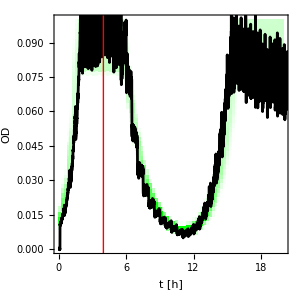

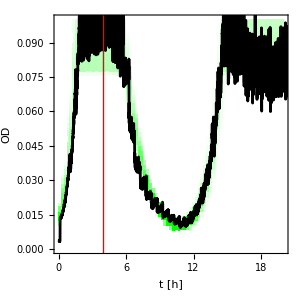

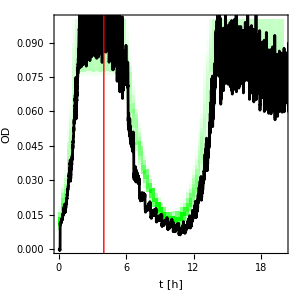

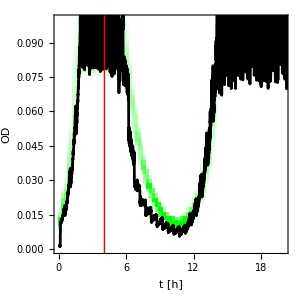

```mathematica
Do[pl=Show[ListDensityPlot[Transpose[BinCounts[Flatten[th[[k,All,All,{1,4}]],1],{0,20,0.25},{0,0.1,0.002}]],ColorFunction->(RGBColor[Max[0,1-2#],1,Max[0,1-2#]]&),PlotRange->All,InterpolationOrder->0,DataRange->{{0,20},{0,0.1}}],ListPlot[dataCIP[[k,"ods"]],Joined->True,PlotStyle->Black],ImageSize->300,BaseStyle->FontSize->24,FrameLabel->{"t [h]","OD"},Epilog->{Red,Line[{{ainjs[[k]],-0.1},{ainjs[[k]],1}}]}];Export[NotebookDirectory[]<>"\\figures\\CIP_spikein_model_and_exp"<>ToString[k]<>".png",pl,"PNG"];Print[pl],{k,1,Length[vols]}]
```

## STR

### rpsL K87R mutant, ratio WT:mutant = 1660:1

```mathematica
{vols,ainjs,births,odinis,birthsres,tregrowths,tfirstthr,ttodecay,tends}=paramsSTR3;
Length[vols]
ainjs
tregrowths
timetostopgrowth=0.66 (* [h] - this models the delayed response to the antibiotic *)
```

4

{4.52511,4.70294,4.88381,4.86339}

{11.0838,11.1479,11.9833,11.5786}

0.66

```mathematica
SetDirectory[NotebookDirectory[]<>"\\models\\STR_standvar"]
Do[
name="START \" \" "<>cmdpars<>" \""<>NotebookDirectory[]<>"models\\turbidostat_standing_variation_for_Bayesian_STR.exe\" standing_var"<>ToString[nn]<>" "<>ToString[vols[[nn]]]<>" "<>ToString[odinis[[nn]]]<>" "<>ToString[births[[nn,1]]]<>" "<>ToString[births[[nn,1]]]<>" "<>ToString[birthsres[[nn,1]]]<>" "<>ToString[ainjs[[nn]]]<>" "<>ToString[tends[[nn]]]<>" "<>(*ToString[tregrowths[[nn]]]*)"100"<>" "<>ToString[odcrit dilf]<>" "<>noreps<>" 0.0006  0.1  0.1 "<>ToString[timetostopgrowth];
Print[name];
Run[name]
,{nn,4}]
SetDirectory[NotebookDirectory[]];
```

C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\STR_standvar

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_STR.exe" standing_var1 25.41 0.00310573 1.98448 1.98448 1.8411 4.52511 20.8075 100 0.075 1000 0.0006  0.1  0.1 0.66

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_STR.exe" standing_var2 26.26 0.0034605 1.91381 1.91381 1.84237 4.70294 20.8076 100 0.075 1000 0.0006  0.1  0.1 0.66

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_STR.exe" standing_var3 24.44 0.00340627 1.82156 1.82156 1.6823 4.88381 20.8076 100 0.075 1000 0.0006  0.1  0.1 0.66

START " "  "C:\Users\bwaclaw\Documents\GitHub\AMR_bioreactor\models\turbidostat_standing_variation_for_Bayesian_STR.exe" standing_var4 26.28 0.00369596 1.87167 1.87167 1.73665 4.86339 20.8077 100 0.075 1000 0.0006  0.1  0.1 0.66

```mathematica
nns=Table[ReadList["models\\STR_standvar\\std_var_n_standing_var"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,4}];
th=Table[Module[{th={},thtmp={}},Do[AppendTo[thtmp,nns[[n,i]]];If[i==Length[nns[[n]]] || nns[[n,i+1,1]]<nns[[n,i,1]],AppendTo[th,thtmp];thtmp={}],{i,Length[nns[[n]]]}];th],{n,Length[nns]}];
Length[#]&/@th
ListPlot[th[[1,1;;10,All,{1,4}]]]

simdist=Table[ReadList["models\\STR_standvar\\std_var_distribution_standing_var"<>ToString[n]<>".dat",{Number,Number,Number,Number}],{n,Length[vols]}];
bestthr=Table[Select[Table[{i,simdist[[k,i,2]]},{i,Length[simdist[[k]]]}],(Abs[#[[2]]-tfirstthr[[k]]]<0.05)&][[All,1]],{k,Length[vols]}]
```

{1000,1000,1000,1000}

#### Distribution of regrowth times (STR)

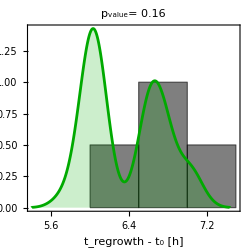

KS-test p-value: 0.157955

```mathematica
Clear[RegrowtTimeDistribution]
RegrowtTimeDistribution[name_]:=Module[{gr,pval,tmp,grth,grexp},
tmp=Flatten[Table[If[NumberQ[#[[1]]],#[[1]]-ainjs[[i]],#]&/@Select[simdist[[i]],(Abs[#[[2]]-tfirstthr[[i]]]<0.1)&],{i,Length[simdist]}]];
grth=SmoothHistogram[Select[tmp,((NumberQ[#])&)][[All]],Automatic,"PDF",PlotStyle->Darker[Green],Filling->Bottom];
grexp=Histogram[Select[tregrowths-ainjs,(#≠∞)&],{4,10,1/2},"PDF",ChartStyle->Opacity[0.5,Black]];
gr=Show[{grexp,grth}(*Epilog->{Red,PointSize[0.02],(Point[{#,0.02}]&/@Select[tregrowths-Ainjs[[All,1,1]],(#≠∞)&])}*),Frame->True,FrameLabel->{"t_regrowth - t_0 [h]",None},AspectRatio->1,ImageSize->250(*,ChartLegends->{"sim","exp"}*),PlotRange->{{4,10},{0,All}},PlotLabel->Style[("p_value= "<>DispPval[KolmogorovSmirnovTest[Select[tmp[[All]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]]]),24]];
Print[gr];
Export[NotebookDirectory[]<>"\\figures\\"<>name,gr,"PNG"];
pval=KolmogorovSmirnovTest[Select[tmp[[All]],NumberQ[#]&],Select[(tregrowths-ainjs),NumberQ[#]&]];
Print["KS-test p-value: ",pval]]

RegrowtTimeDistribution["STR3_spike_in_Pregrowth.png"]
```

### OD vs time curves - experiment and modelling:

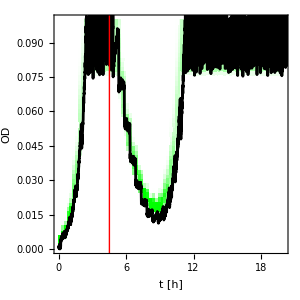

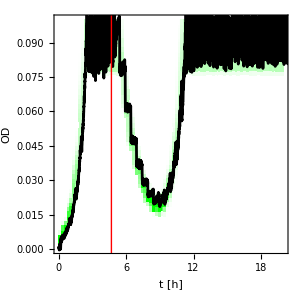

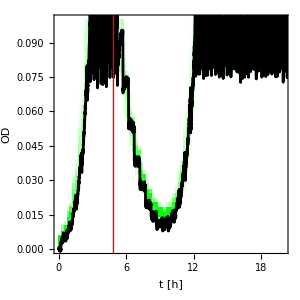

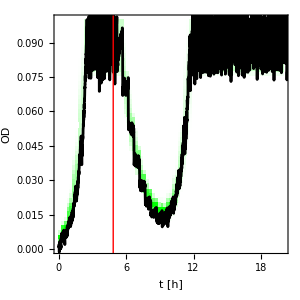

```mathematica
Do[pl=Show[ListDensityPlot[Transpose[BinCounts[Flatten[th[[k,All,All,{1,4}]],1],{0,20,0.25},{0,0.1,0.002}]],ColorFunction->(RGBColor[Max[0,1-2#],1,Max[0,1-2#]]&),PlotRange->All,InterpolationOrder->0,DataRange->{{0,20},{0,0.1}}],ListPlot[dataSTR3[[k,"ods"]],Joined->True,PlotStyle->Black],ImageSize->300,BaseStyle->FontSize->24,FrameLabel->{"t [h]","OD"},Epilog->{Red,Line[{{ainjs[[k]],-0.1},{ainjs[[k]],1}}]}];Export[NotebookDirectory[]<>"\\figures\\STR3_spikein_model_and_exp"<>ToString[k]<>".png",pl,"PNG"];Print[pl],{k,1,Length[vols]}]
```